## Index Reset

```mathematica
(*Get the current Notebook*)
nb=EvaluationNotebook[];
(*Iterate through all cells and reset numbering*)
Module[{cells,count=1},
(*Get all cells in the notebook*)
cells=Cells[nb];
Do[
(*Set new numbering*)
SetOptions[cell,CellLabel->ToString[count]<>". "];
(*Increment the counter for the next cell*)
count++,
(*Loop over all cells*)
{cell,cells} 
]];
```

# Graphs & Networks

## Construction and Representation



```mathematica
Graph[{1<->2,2<->3,3<->1}]
```



```mathematica
Graph[{1->2,2->3,3->1}]
```

```mathematica
Graph[Table[i->Mod[i^2,74],{i,100}]]
```

-Graphics-

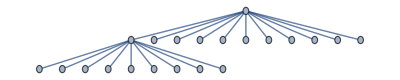

```mathematica
g=Graph[Table[i<->Mod[i+1,2],{i,20}]]
```

```mathematica
Graph[{Style[1<->2,Red],Style[1<->2,Blue],2<->3,3<->1}]
```

#### DirectedGraph

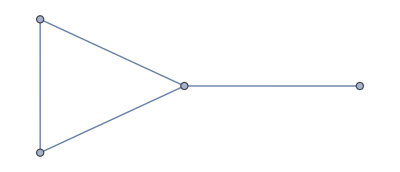
```mathematica
DirectedGraph[-Graphics-]
```

-Graphics-

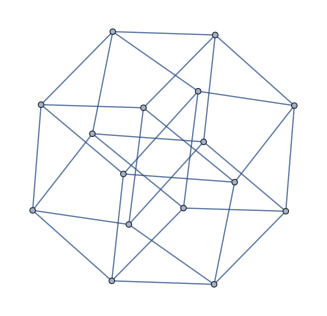
```mathematica
DirectedGraph[-Graphics-]
```

-Graphics-

#### PathGraph



```mathematica
graph1 = PathGraph[{a,b,c}]
```

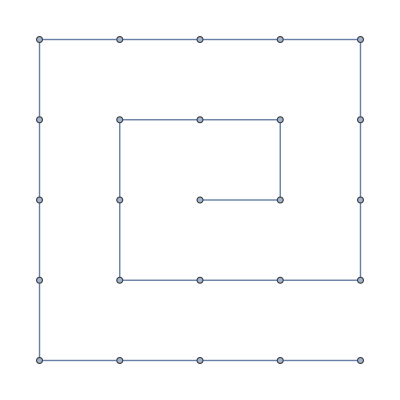

```mathematica
graph2 = PathGraph[Range[25]]
```

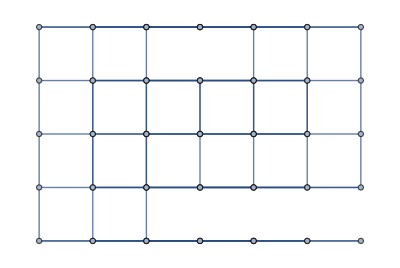

```mathematica
GraphProduct[graph1, graph2]
```

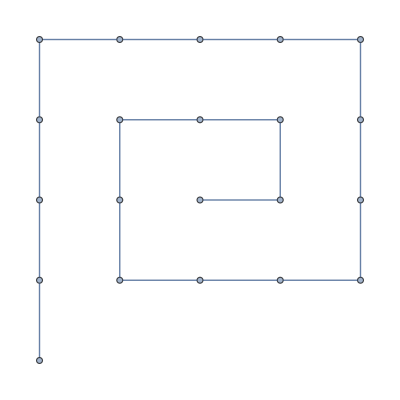

```mathematica
PathGraph[Table[i<->i+1,{i,20}]]
```

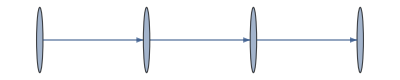

```mathematica
PathGraph[{1->2,2->3,3->4},EdgeStyle->Arrowheads[Medium]]
```

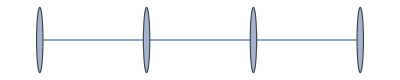

```mathematica
PathGraph[{1->2,2->3,3->4},DirectedEdges->False]
```

```mathematica
{PathGraph[{1->2,2->3,3->4},EdgeStyle->Arrowheads[Medium]],PathGraph[{1<->2,2<->3,3<->4}]}
```

{-Graphics-,-Graphics-}

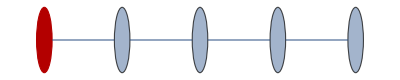

```mathematica
PathGraph[Range[5],VertexSize->Medium,GraphHighlight->{1}]
```

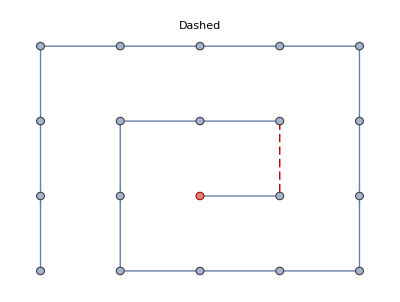
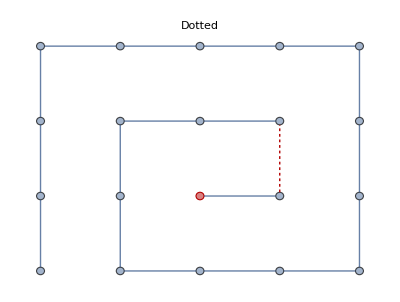
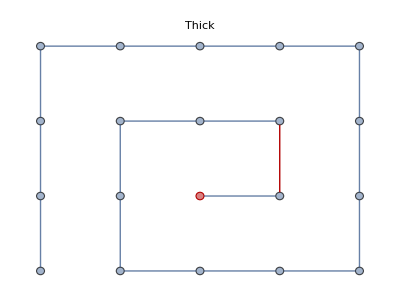
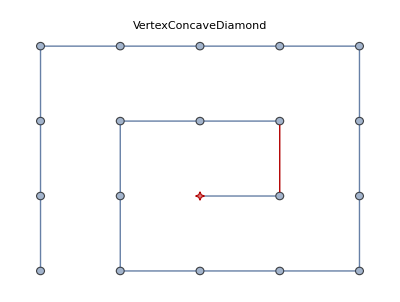
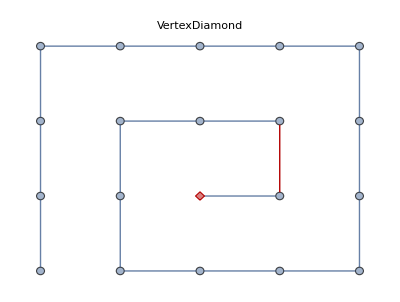
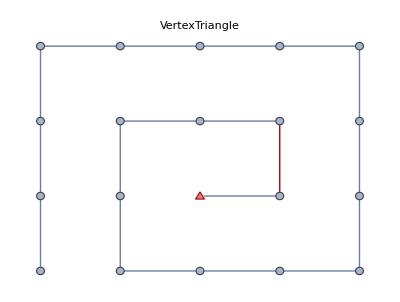
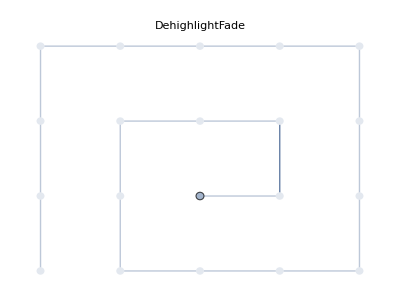
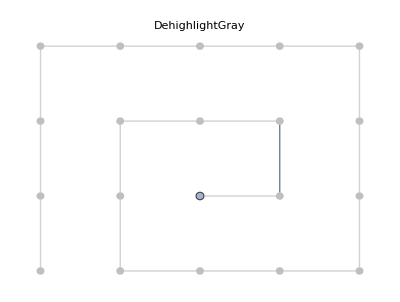

```mathematica
PathGraph[Range[20],GraphHighlight->{1,2<->3},VertexSize->Small,GraphHighlightStyle->#,PlotLabel->#]&/@Select[ResourceData["GraphHighlightStyle"],#=!=Automatic&]
```

```mathematica
PathGraph[Range[20],PlotTheme->"LargeGraph"]
```

-Graphics-

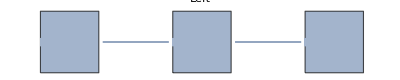
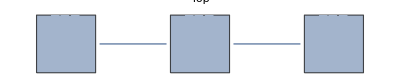
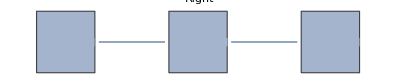
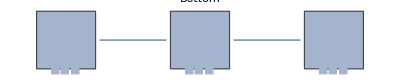

```mathematica
Table[PathGraph[Range[3],VertexSize->0.5,VertexLabels->Table[i->Placed["■■■",p],{i,3}],VertexShapeFunction->"Square",PlotLabel->p],{p,{Left,Top,Right,Bottom}}]
```

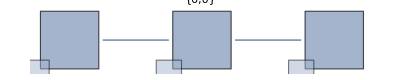
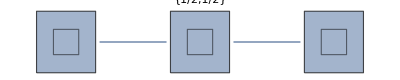
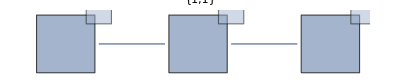

```mathematica
Table[
PathGraph[
Range[3], VertexSize -> 0.5, 
VertexShapeFunction -> "Square", 
VertexLabels -> Table[i -> Placed[-Graphics-, p], {i, 3}], 
PlotLabel -> p, 
BaselinePosition -> Bottom
], 
{p, {{0, 0}, {1/2, 1/2}, {1, 1}}}
]
```

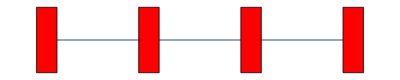

```mathematica
vf2[{xc_,yc_},name_,{w_,h_}]:={Red,Rectangle[{xc-w,yc-h},{xc+w,yc+h}]}
PathGraph[Range[4],VertexSize->0.2,VertexStyle->Blue,VertexShapeFunction->vf2]
```

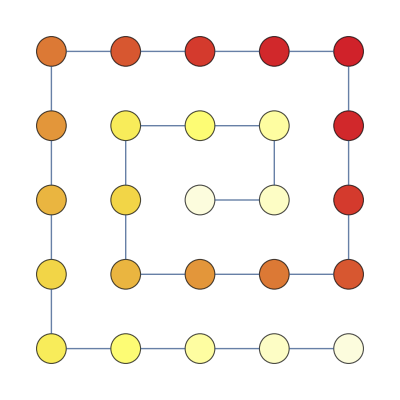

```mathematica
HighlightCentrality[g_,cc_]:=HighlightGraph[g,Table[Style[VertexList[g][[i]],ColorData["TemperatureMap"][cc[[i]]/Max[cc]]],{i,VertexCount[g]}]];
g=PathGraph[Range[25],VertexSize->Large];
HighlightCentrality[g,ClosenessCentrality[g]]
```

## Visualization

### Graph Layoutshttps://reference.wolfram.com/language/guide/GraphLayouts.htmlNonehttps://reference.wolfram.com/language/guide/GraphLayouts.htmlHyperlinkActionRecycledHyperlinkActive

```mathematica
GraphPlot3D[{"start"->"none",Labeled["none"->"none","other"],Labeled["none"->"slash","/"],Labeled["slash"->"none","other"],Labeled["slash"->"C++","/"],Labeled["slash"->"C","*"],Labeled["C++"->"C++","other"],Labeled["C++"->"none","end-of-line"],Labeled["C"->"C","other"],Labeled["C"->"star","*"],Labeled["star"->"star","*"],Labeled["star"->"C","other"],Labeled["star"->"none","/"]},DirectedEdges->True,PlotTheme->"DiagramBlue"]
```

-Graphics3D-

```mathematica
GraphPlot3D[ExampleData[{"Matrix","HB/can_292"},"Matrix"]]
```

-Graphics3D-

```mathematica
w=Characters["Shakespeare"];
GraphPlot[Thread[Drop[w,-1]->Drop[w,1]],PlotTheme->"ClassicDiagram",DirectedEdges->True]
```

-Graphics-

```mathematica
GraphPlot3D[ExampleData[{"Matrix","HB/dwt_1005"},"Matrix"],VertexShapeFunction->None]
```

-Graphics3D-

### LayeredGraphPlot

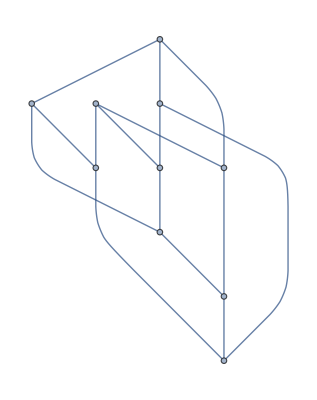

```mathematica
LayeredGraphPlot[PetersenGraph[]]
```

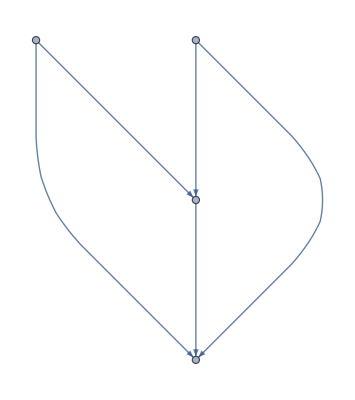

```mathematica
LayeredGraphPlot[{1->2,3->1,3->2,4->1,4->2}]
```

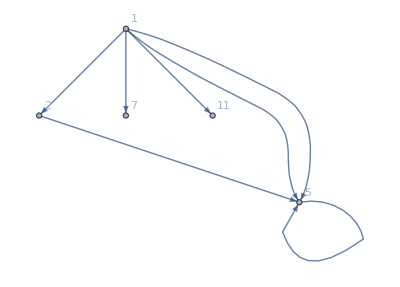

```mathematica
LayeredGraphPlot[{1->2,1->7,1->11,2->5,1->5,5->5,1->5},VertexLabels->Automatic]
```

```mathematica
Table[Framed@LayeredGraphPlot[Table[i->Mod[i^2,31],{i,0,31}],GraphLayout->{"PackingLayout"->pm}],{pm,{Automatic,"ClosestPacking"}}]
```

{-Graphics-,-Graphics-}

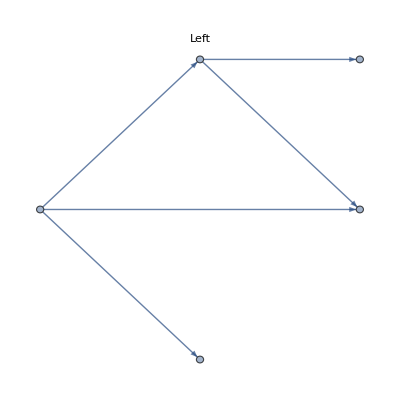
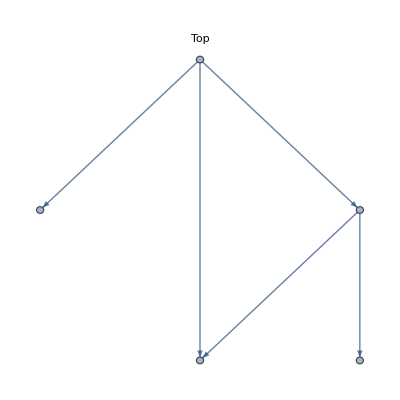
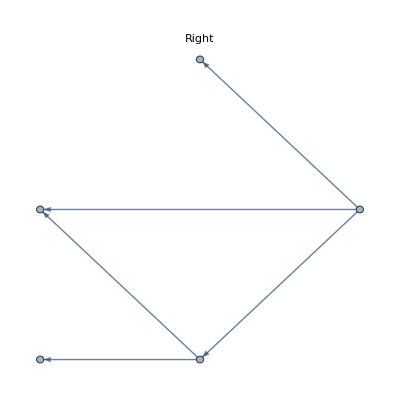
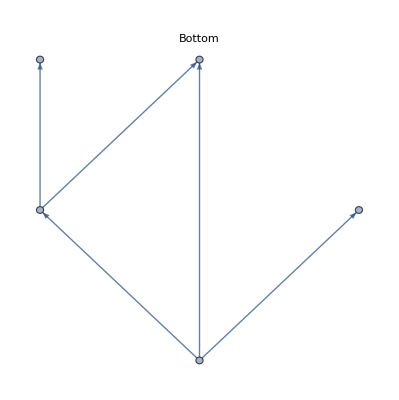

```mathematica
Row@Table[LayeredGraphPlot[{1->3,1->4,1->5,3->5,3->6},pos,PlotLabel->pos],{pos,{Left,Top,Right,Bottom}}]
```

```mathematica
f[x_]:=Module[{e1,e2,e3},e1=x+1;e2=Exp[x e1]+1;
e3=e1+Sin[x e2];x+e3+e1]
LayeredGraphPlot[{x->f,e3->f,e1->f,e1->e3,x->e3,e2->e3,x->e2,e1->e2,x->e1},PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
g={"5th Edition"->"6th Edition","5th Edition"->"PWB 1.0","6th Edition"->"1 BSD","6th Edition"->"Interdata","6th Edition"->"LSX","6th Edition"->"Mini Unix","6th Edition"->"Wollongong","PWB 1.0"->"PWB 1.2","PWB 1.0"->"USG 1.0","1 BSD"->"2 BSD","Interdata"->"PWB 2.0","Interdata"->"Unix/TS 3.0","Interdata"->"7th Edition","PWB 1.2"->"PWB 2.0","USG 1.0"->"USG 2.0","USG 1.0"->"CB Unix 1","7th Edition"->"2 BSD","7th Edition"->"32V","7th Edition"->"Xenix","7th Edition"->"Ultrix-11","7th Edition"->"UniPlus+","7th Edition"->"V7M","PWB 2.0"->"Unix/TS 3.0","USG 2.0"->"USG 3.0","CB Unix 1"->"CB Unix 2","32V"->"3 BSD","Unix/TS 1.0"->"Unix/TS 3.0","USG 3.0"->"Unix/TS 3.0","CB Unix 2"->"CB Unix 3","3 BSD"->"4 BSD","V7M"->"Ultrix-11","Unix/TS 3.0"->"TS 4.0","CB Unix 3"->"Unix/TS++","CB Unix 3"->"PDP-11 Sys V","4 BSD"->"4.1 BSD","Unix/TS++"->"TS 4.0","4.1 BSD"->"8th Edition","4.1 BSD"->"4.2 BSD","4.1 BSD"->"2.8 BSD","2 BSD"->"2.8 BSD","TS 4.0"->"System V.0","4.2 BSD"->"4.3 BSD","4.2 BSD"->"Ultrix-32","2.8 BSD"->"2.9 BSD","2.8 BSD"->"Ultrix-11","System V.0"->"System V.2","8th Edition"->"9th Edition","System V.2"->"System V.3"};
LayeredGraphPlot[g,PlotTheme->"ClassicDiagram",VertexSize->{.5,.1}]
```

-Graphics-

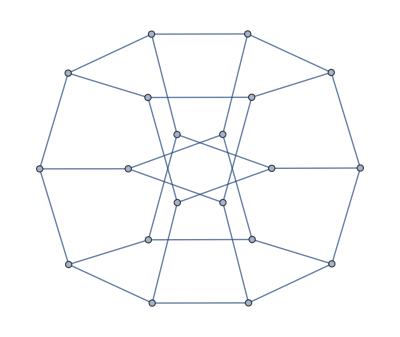
{-Graphics-,-Graphics3D-}

```mathematica
g={1->2,1->6,1->20,2->3,2->17,3->4,3->12,4->5,4->15,5->6,5->10,6->7,7->8,7->16,8->9,8->19,9->10,9->14,10->11,11->12,11->20,12->13,13->14,13->18,14->15,15->16,16->17,17->18,18->19,19->20};
{GraphPlot[g],GraphPlot3D[g]}
```

```mathematica
DaughterNuclides[s_List]:=DeleteCases[Union[Apply[Join,Map[IsotopeData[#,"DaughterNuclides"]&,DeleteCases[s,_Missing]]]],_Missing]
ReachableNuclides[s_List]:=FixedPoint[Union[Join[#,DaughterNuclides[#]]]&,s]
DecayNetwork[iso_List]:=Apply[Join,Map[Thread[#->DaughterNuclides[{#}]]&,ReachableNuclides[iso]]]
DecayNetworkPlot[s_]:=LayeredGraphPlot[Map[IsotopeData[#,"Symbol"]&,DecayNetwork[{s}],{2}],PerformanceGoal->"Quality",VertexShapeFunction->(Text[Framed[Style[#2,8,Black],Background->LightYellow],#1]&)]
DecayNetworkPlot["Uranium235"]
```

-Graphics-

```mathematica
DecayNetworkPlot["Polonium189"]
```

-Graphics-

```mathematica
DecayNetworkPlot["Plutonium239"]
```

## Computation on Graphs

### Graph Operations and Modifications

#### Subgraph

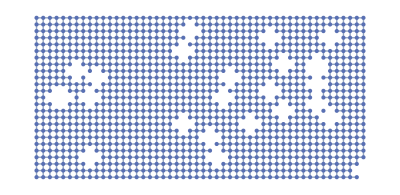

```mathematica
g = GridGraph[{25, 50}];
Subgraph[g,Complement[VertexList[g],VertexComponent[g,RandomSample[VertexList[g],25],1]],AnnotationRules->Inherited]
```